```mathematica
(*Created 2015 by CunhaJ 
The aim of this notebook is to study regimes of validity of thermionic emission vs field emission in GaAs following Murphy-Good (MG) theory 
https://journals.aps.org/pr/abstract/10.1103/PhysRev.102.1464 *)
```

```mathematica
(*Emission from Tungsten W*)
```

```mathematica
(*physical constants*)
kB= 8.62*10^(-5) (*eV/K*);
q=1.6*10^(-19) (*C*);
me=9.1*10^(-31) (*kg*);
ep0=8.85*10^(-12)(*/m*);
hbar=6.58*10^(-16)(*eV.s*);
phi=4.5(*workfunction for tungsten in eV*);
Q=q^2/ (16*Pi*ep0)(*Image Force constant*)
```

5.75476×10^-29

```mathematica
(*Thermionic Emission -> Richardson-Dushman (RD) Equation; 
Field Emission -> Fowler-Nordheim (FN) Equation*)
```

```mathematica
(*Limits of RD and FN equations following MG*)
FRDmax[T_]:=(Sqrt[2*me]*kB*T/(10*hbar))^(4/3)*Q^(1/3)
FNmax[T_]:=kB*T/(4*Q)*(phi/(kB*T)-6)^2
FNmin[T_]:=4*kB*T*Sqrt[2*me*phi]/hbar
```

```mathematica
FRDmax[100]
```

8.24958×10^-14

```mathematica
(*Murphy-Good paper uses Hartree units
https://en.wikipedia.org/wiki/Atomic_units*)
paperF[field_]:=field/(5.15*10^9);(*V/cm*)
paperj[current_]:=current/(2.37*10^14 );(*A.cm-2*)
paperE[energy_]:=energy/(27.2);(*eV*)
```

```mathematica
(*Insert Field in V/cm and Temperature in Kelvin*)
dfunction[Freal_,Treal_]:=paperF[Freal]^(3/4)/(Pi*paperE[kB*Treal])
```

```mathematica
(*Upper limit of thermionic emission at d=1*)
Solve[dfunction[Freal,Treal]==1,{Treal,Freal}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Freal→(-551.52-955.261 ⅈ) Treal^(4/3)},{Freal→(-551.52+955.261 ⅈ) Treal^(4/3)},{Freal→1103.04 Treal^(4/3)}}

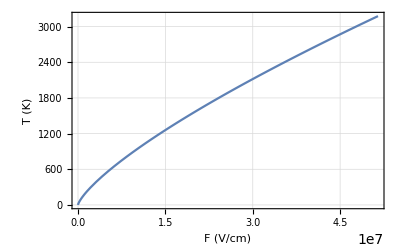

```mathematica
(*Plot OK*)
Plot[{(Freal/1103.04)^(3/4)} ,{Freal,0,5.15*10^7},Frame-> True,FrameLabel-> {"F (V/cm)","T (K)"}, GridLines-> Automatic, GridLinesStyle->Directive[Dotted, Gray]]
```

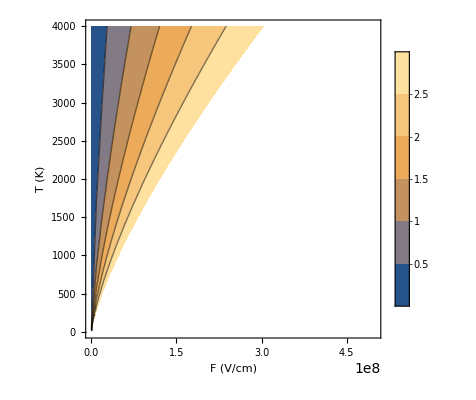

```mathematica
ContourPlot[Re[dfunction[Freal,Treal]],{Freal,0,5*10^8},{Treal,0,4000},PlotLegends-> Automatic,PlotRange-> {0,3},FrameLabel-> {"F (V/cm)", "T (K)"}]
```

```mathematica
function1[Freal_,Treal_]:=Log[(1-dfunction[Freal,Treal])/dfunction[Freal,Treal]]-1/(dfunction[Freal,Treal]*(1-dfunction[Freal,Treal]));
(*BE CAREFUL, the workfunction have to be written in STRANGE units as well!!!*)
function2[Freal_,Treal_,phi_]:=-Pi*paperF[Freal]^(-3/4)*(phi-Sqrt[paperF[Freal]]);
```

```mathematica
function3[Freal_,Treal_]=Log[(1-dfunction[Freal,Treal])/dfunction[Freal,Treal]]-1/(1-dfunction[Freal,Treal]);
function4[Freal_,Treal_]=-Pi*paperF[ Freal]^(-1/8);
```

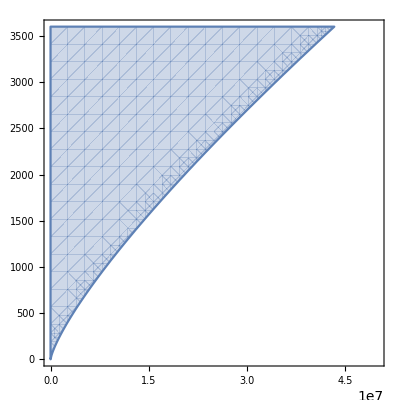

```mathematica
RegionPlot[{Re[function3[Freal,Treal]]> function4[Freal,Treal]&&Treal>(Freal/1103.04)^(3/4)}, {Freal,0,5*10^7},{Treal,0,3600},WorkingPrecision->164]
```

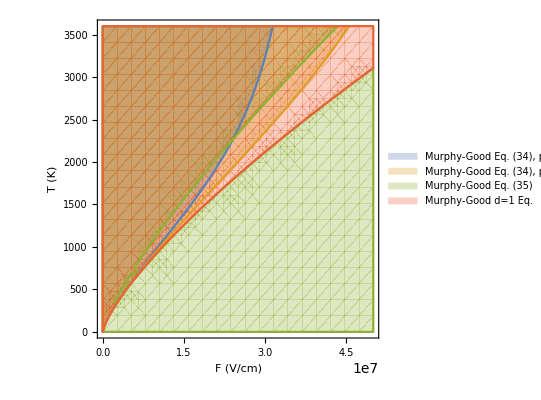

```mathematica
RegionPlot[{Re[function1[Freal,Treal]]> function2[Freal,Treal,paperE[3]]&&Treal>(Freal/1103.04)^(3/4),
Re[function1[Freal,Treal]]> function2[Freal,Treal,paperE[4.5]]&&Treal>(Freal/1103.04)^(3/4),
Re[function3[Freal,Treal]]> function4[Freal,Treal],Treal>(Freal/1103.04)^(3/4)}, {Freal,0,5*10^7},{Treal,0,3600}, WorkingPrecision-> 256,FrameLabel->{"F (V/cm)","T (K)"},PlotLegends-> {"Murphy-Good Eq. (34), phi=3eV","Murphy-Good Eq. (34), phi=3eV","Murphy-Good Eq. (35)", "Murphy-Good d=1 Eq."}]
```

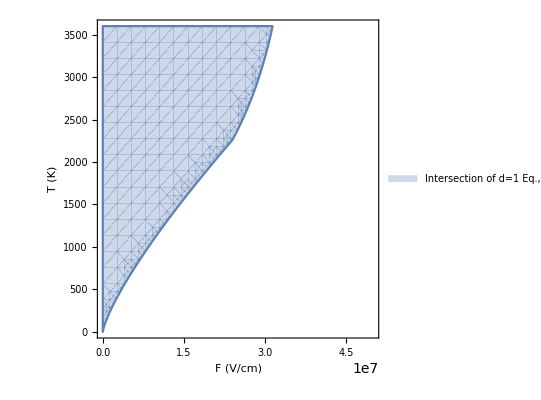

```mathematica
RegionPlot[{Re[function1[Freal,Treal]]> function2[Freal,Treal,paperE[3]]&&Treal>(Freal/1103.04)^(3/4)&&Re[function3[Freal,Treal]]> function4[Freal,Treal]&&Treal>(Freal/1103.04)^(3/4)}, {Freal,0,5*10^7},{Treal,0,3600}, WorkingPrecision-> 256,FrameLabel->{"F (V/cm)","T (K)"},PlotLegends-> {"Intersection of d=1 Eq., Eq.(34) and Eq.(35) for phi=3eV"}]
```

```mathematica
(*FIELD EMISSION REGION CALCULATION FOLLOWING MURPHY AND GOOD*)
```

```mathematica
(*Exploratory field emission formula - not important for the case
ATTENTION v(y) and t(y) were taken from the Forbes app, see JENSEN 2007 "Electron Emission Physics" page 88*)
t[y_]:=1+0.06489*y+0.0458308*y^2
v[y_ ]:=0.936814-y^2
c[Freal_,phi_]:=2*Sqrt[2*paperE[phi]]*t[Sqrt[paperF[Freal]]/paperE[phi]]/paperF[Freal]
f[Freal_,phi_]:=(Sqrt[2]/2)*(paperE[phi]^(3/2)/(paperF[Freal]*(paperE[phi]^2-paperF[Freal])))*v[Sqrt[paperF[Freal]]/paperE[phi]]
```

```mathematica
JT=Table[{y,v[y],t[y]},{y,0,1,0.05}]//TableForm
```

0. | 0.936814 | 1.
0.05 | 0.934314 | 1.00336
0.1 | 0.926814 | 1.00695
0.15 | 0.914314 | 1.01076
0.2 | 0.896814 | 1.01481
0.25 | 0.874314 | 1.01909
0.3 | 0.846814 | 1.02359
0.35 | 0.814314 | 1.02833
0.4 | 0.776814 | 1.03329
0.45 | 0.734314 | 1.03848
0.5 | 0.686814 | 1.0439
0.55 | 0.634314 | 1.04955
0.6 | 0.576814 | 1.05543
0.65 | 0.514314 | 1.06154
0.7 | 0.446814 | 1.06788
0.75 | 0.374314 | 1.07445
0.8 | 0.296814 | 1.08124
0.85 | 0.214314 | 1.08827
0.9 | 0.126814 | 1.09552
0.95 | 0.034314 | 1.10301
1. | -0.063186 | 1.11072

```mathematica
(*Definition of v(y) and s(y) using the Houston tables https://journals.aps.org/pr/abstract/10.1103/PhysRev.90.515
*)
A={
{0,1,1},
{0.05,0.9948,0.9995},
{0.1,0.9817,0.9981},
{0.15,0.9622,0.9958},
{0.2,0.9370,0.9926},
{0.25,0.9068,0.9885},
{0.3,0.8718,0.9835},
{0.35,0.8323,0.9777},
{0.4,0.7888,0.9711},
{0.45,0.7413,0.9637},
{0.5,0.69,0.9554},
{0.55,0.6351,0.9464},
{0.6,0.5768,0.9366},
{0.65,0.5152,0.9261},
{0.7,0.4504,0.9149},
{0.75,0.3825,0.9030},
{0.8,0.3117,0.8903},
{0.85,0.2379,0.8770},
{0.9,0.1613,0.8630},
{0.95,0.0820,0.8483},
{1,0,0.833}
};
```

```mathematica
valuesy=ConstantArray[0,20];
valuesv=ConstantArray[0,20];
valuess=ConstantArray[0,20];
valuesyv=Table[0,{i,1,20},{j,1,2}];
valuesys=Table[0,{i,1,20},{j,1,2}];
valuesyt=Table[0,{i,1,20},{j,1,2}];
```

```mathematica
valuesy=A[[All,1]]
valuesv=A[[All,2]]
valuess=A[[All,3]]
valuesyv=A[[All,{1,2}]]
valuesys=A[[All,{1,3}]]
valuesyt=A[[All,{1,2}]]
```

{0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1}

{1,0.9948,0.9817,0.9622,0.937,0.9068,0.8718,0.8323,0.7888,0.7413,0.69,0.6351,0.5768,0.5152,0.4504,0.3825,0.3117,0.2379,0.1613,0.082,0}

{1,0.9995,0.9981,0.9958,0.9926,0.9885,0.9835,0.9777,0.9711,0.9637,0.9554,0.9464,0.9366,0.9261,0.9149,0.903,0.8903,0.877,0.863,0.8483,0.833}

{{0,1},{0.05,0.9948},{0.1,0.9817},{0.15,0.9622},{0.2,0.937},{0.25,0.9068},{0.3,0.8718},{0.35,0.8323},{0.4,0.7888},{0.45,0.7413},{0.5,0.69},{0.55,0.6351},{0.6,0.5768},{0.65,0.5152},{0.7,0.4504},{0.75,0.3825},{0.8,0.3117},{0.85,0.2379},{0.9,0.1613},{0.95,0.082},{1,0}}

{{0,1},{0.05,0.9995},{0.1,0.9981},{0.15,0.9958},{0.2,0.9926},{0.25,0.9885},{0.3,0.9835},{0.35,0.9777},{0.4,0.9711},{0.45,0.9637},{0.5,0.9554},{0.55,0.9464},{0.6,0.9366},{0.65,0.9261},{0.7,0.9149},{0.75,0.903},{0.8,0.8903},{0.85,0.877},{0.9,0.863},{0.95,0.8483},{1,0.833}}

{{0,1},{0.05,0.9948},{0.1,0.9817},{0.15,0.9622},{0.2,0.937},{0.25,0.9068},{0.3,0.8718},{0.35,0.8323},{0.4,0.7888},{0.45,0.7413},{0.5,0.69},{0.55,0.6351},{0.6,0.5768},{0.65,0.5152},{0.7,0.4504},{0.75,0.3825},{0.8,0.3117},{0.85,0.2379},{0.9,0.1613},{0.95,0.082},{1,0}}

```mathematica
valuesyt[[All,2]]=(4*A[[All,3]]-A[[All,2]])/3
```

{1,1.00107,1.00357,1.007,1.01113,1.01573,1.02073,1.02617,1.03187,1.03783,1.04387,1.05017,1.05653,1.06307,1.06973,1.0765,1.08317,1.09003,1.0969,1.10373,1.11067}

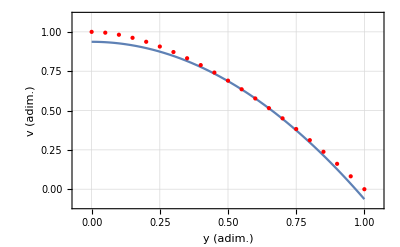

```mathematica
Plot[v[y],{y,0,1},Frame-> True, Epilog->{PointSize[Medium],Red,Point[valuesyv]},PlotRange-> {{-0.05,1.05},{-.1,1.1}}, FrameLabel-> {"y (adim.)","v (adim.)"},GridLines->Automatic]
```

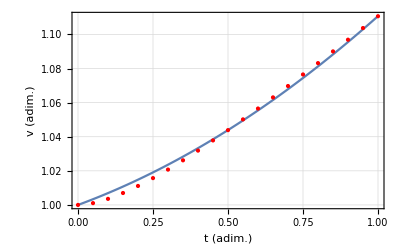

```mathematica
Plot[t[y],{y,0,1},Frame-> True, Epilog->{PointSize[Medium],Red,Point[valuesyt]},PlotRange-> Automatic, FrameLabel-> {"t (adim.)","v (adim.)"},GridLines->Automatic]
```

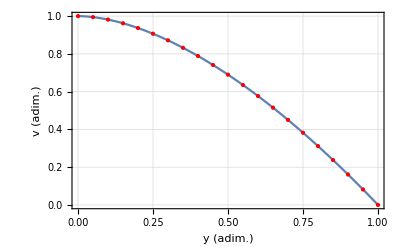

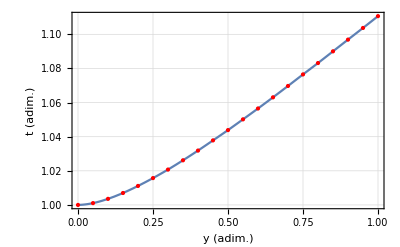

```mathematica
(*INTERPOLATION OF THE FUNCTIONS v(y) and t(y) from the Burgess-Kroemer-Houston paper https://journals.aps.org/pr/abstract/10.1103/PhysRev.90.515*)
ifunv=Interpolation[valuesyv];
ifunt=Interpolation[valuesyt];
Plot[ifunv[y],{y,0,1},Epilog->{PointSize[Medium],Red,Point[valuesyv]},Frame->True,FrameLabel-> {"y (adim.)","v (adim.)"},GridLines-> Automatic]
Plot[ifunt[y],{y,0,1},Epilog->{PointSize[Medium],Red,Point[valuesyt]},Frame->True,FrameLabel-> {"y (adim.)","t (adim.)"},GridLines-> Automatic]
```

```mathematica
(*FN formulas*)
functionFN1[Freal_,Treal_,phi_]:=paperE[phi]-Sqrt[paperF[Freal]]
functionFN2[Freal_,Treal_,phi_]:=(paperF[Freal]^(3/4))/Pi+paperE[kB*Treal]/(1-c[Freal,phi]*paperE[kB*Treal])
functionFN3[Freal_,Treal_,phi_]:=1-c[Freal,phi]*paperE[kB*Treal]
functionFN4[Freal_,Treal_,phi_]:=Sqrt[2*f[Freal,phi]]*paperE[kB*Treal]
```

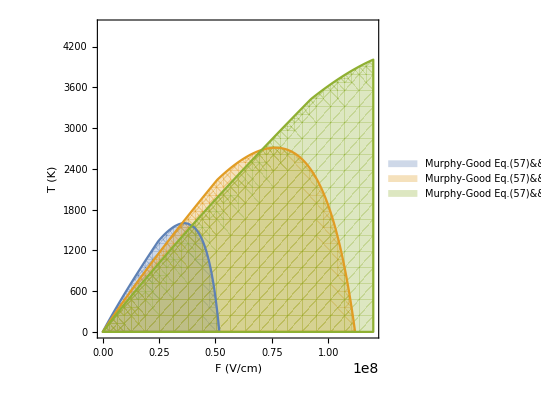

```mathematica
RegionPlot[
{
Re[functionFN1[Freal,Treal,3]]> functionFN2[Freal,Treal,3]&&Re[functionFN3[Freal,Treal,3]]> functionFN4[Freal,Treal,3],
Re[functionFN1[Freal,Treal,4.5]]> functionFN2[Freal,Treal,4.5]&&Re[functionFN3[Freal,Treal,4.5]]> functionFN4[Freal,Treal,4.5],
Re[functionFN1[Freal,Treal,6.3]]> functionFN2[Freal,Treal,6.3]&&Re[functionFN3[Freal,Treal,6.3]]> functionFN4[Freal,Treal,6.3]
}, 
{Freal,0,12*10^7},{Treal,0,4500}, WorkingPrecision-> 32,FrameLabel->{"F (V/cm)","T (K)"},PlotLegends-> {"Murphy-Good Eq.(57)&&Eq.(58), phi=3 eV","Murphy-Good Eq.(57)&&Eq.(58), phi=4.5 eV","Murphy-Good Eq.(57)&&Eq.(58), phi=6.3 eV"  }]
```

```mathematica
RegionPlot[{Re[functionFN1[Freal,Treal,phi]]> functionFN2[Freal,Treal,phi]}, {Freal,0,12*10^7},{Treal,4500}, WorkingPrecision-> 256,FrameLabel->{"F (V/cm)","T (K)"},PlotLegends-> {"Intersection of d=1 Eq., Eq.(34) and Eq.(35) for phi=3eV"}]
```

RegionPlot::pllim: Range specification {Treal, 4500} is not of the form {x, xmin, xmax}.

RegionPlot[{Re[functionFN1[Freal,Treal,phi]]>functionFN2[Freal,Treal,phi]},{Freal,0,12 10^7},{Treal,4500},WorkingPrecision→256,FrameLabel→{F (V/cm),T (K)},PlotLegends→{Intersection of d=1 Eq., Eq.(34) and Eq.(35) for phi=3eV}]

```mathematica
functionFN3[a,c,b]
```

1-(8851.28 (1+(6.58397×10^-9 a)/b^2+(0.0000245948 √a)/b) √b c)/a

```mathematica
functionFN1[a,b,c]//N
```

-0.0000139347 √a+0.0367647 c

```mathematica
(*LETS TRY TO USE THE v AND t INTERPOLATIONS*)
```

```mathematica
t[y_]:=ifunt[y]
v[y_ ]:=ifunv[y]
```

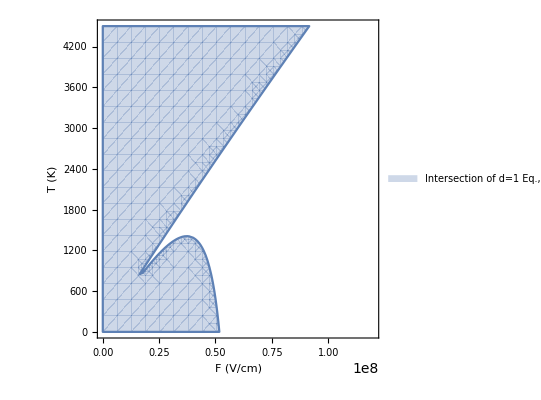

```mathematica
RegionPlot[{Re[functionFN1[Freal,Treal,3]]> functionFN2[Freal,Treal,phi]}, {Freal,0,12*10^7},{Treal,0,4500}, WorkingPrecision-> 256,FrameLabel->{"F (V/cm)","T (K)"},PlotLegends-> {"Intersection of d=1 Eq., Eq.(34) and Eq.(35) for phi=3eV"}]
```

```mathematica
(*The use of the interpolation seems to give different result*)
```

InterpolatingFunction::dmval: Input value {1.00406} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.05306} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.09989} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

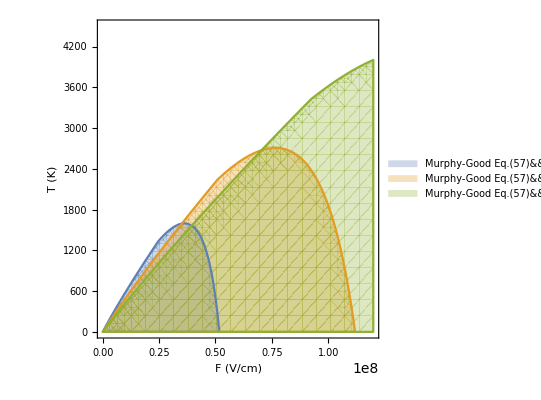

```mathematica
RegionPlot[
{
Re[functionFN1[Freal,Treal,3]]> functionFN2[Freal,Treal,3]&&Re[functionFN3[Freal,Treal,3]]> functionFN4[Freal,Treal,3],
Re[functionFN1[Freal,Treal,4.5]]> functionFN2[Freal,Treal,4.5]&&Re[functionFN3[Freal,Treal,4.5]]> functionFN4[Freal,Treal,4.5],
Re[functionFN1[Freal,Treal,6.3]]> functionFN2[Freal,Treal,6.3]&&Re[functionFN3[Freal,Treal,6.3]]> functionFN4[Freal,Treal,6.3]
}, 
{Freal,0,12*10^7},{Treal,0,4500}, WorkingPrecision-> 32,FrameLabel->{"F (V/cm)","T (K)"},PlotLegends-> {"Murphy-Good Eq.(57)&&Eq.(58), phi=3 eV","Murphy-Good Eq.(57)&&Eq.(58), phi=4.5 eV","Murphy-Good Eq.(57)&&Eq.(58), phi=6.3 eV"  }]
```

```mathematica
(*BOTH REGIONS PRESENTED ION THE SAME PLOT*)
```

3

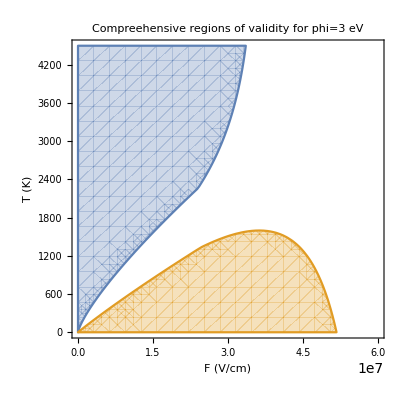

```mathematica
phi=3 (*eV*)
RegionPlot[
{Re[function1[Freal,Treal]]> function2[Freal,Treal,paperE[phi]]&&Treal>(Freal/1103.04)^(3/4)&&Re[function3[Freal,Treal]]> function4[Freal,Treal]&&Treal>(Freal/1103.04)^(3/4),
Re[functionFN1[Freal,Treal,phi]]> functionFN2[Freal,Treal,phi]&&Re[functionFN3[Freal,Treal,phi]]> functionFN4[Freal,Treal,phi]
}, 
{Freal,0,6*10^7},{Treal,0,4500}, 
WorkingPrecision-> 32,FrameLabel->{"F (V/cm)","T (K)"},PlotLabel->"Compreehensive regions of validity for phi=3 eV\n"]
```

4.5

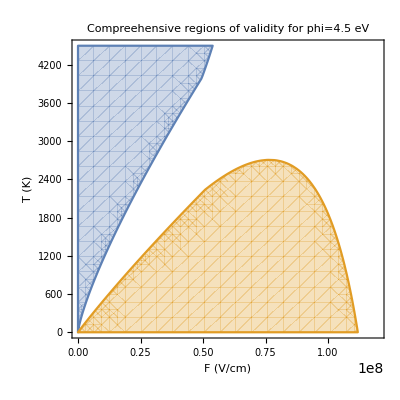

```mathematica
phi=4.5 (*eV*)
RegionPlot[
{Re[function1[Freal,Treal]]> function2[Freal,Treal,paperE[phi]]&&Treal>(Freal/1103.04)^(3/4)&&Re[function3[Freal,Treal]]> function4[Freal,Treal]&&Treal>(Freal/1103.04)^(3/4),
Re[functionFN1[Freal,Treal,phi]]> functionFN2[Freal,Treal,phi]&&Re[functionFN3[Freal,Treal,phi]]> functionFN4[Freal,Treal,phi]
}, 
{Freal,0,12*10^7},{Treal,0,4500}, 
WorkingPrecision-> 32,FrameLabel->{"F (V/cm)","T (K)"},PlotLabel->"Compreehensive regions of validity for phi=4.5 eV\n"]
```

6.3

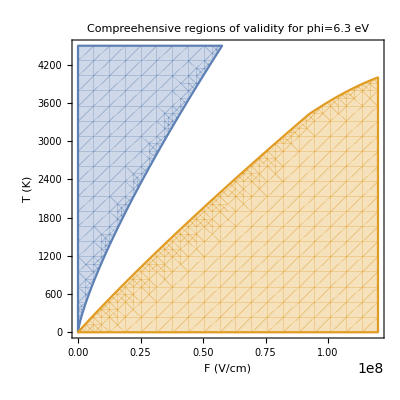

```mathematica
phi=6.3 (*eV*)
RegionPlot[
{Re[function1[Freal,Treal]]> function2[Freal,Treal,paperE[phi]]&&Treal>(Freal/1103.04)^(3/4)&&Re[function3[Freal,Treal]]> function4[Freal,Treal]&&Treal>(Freal/1103.04)^(3/4),
Re[functionFN1[Freal,Treal,phi]]> functionFN2[Freal,Treal,phi]&&Re[functionFN3[Freal,Treal,phi]]> functionFN4[Freal,Treal,phi]
}, 
{Freal,0,12*10^7},{Treal,0,4500}, 
WorkingPrecision-> 32,FrameLabel->{"F (V/cm)","T (K)"},PlotLabel->"Compreehensive regions of validity for phi=6.3 eV\n"]
```

```mathematica
(*Definition of the CURRENT DENSITY*)
```

```mathematica
(*Re-definition of auxiliary functions to avoid interpolation problems *)
t[y_]:=1+0.06489*y+0.0458308*y^2
v[y_ ]:=0.936814-y^2
```

```mathematica
(*Thermionic Current from Murphy-Good*)
jMGRD[Freal_,Treal_,phi_]:=0.5*(paperE[kB*Treal]/Pi)^2*(Pi*dfunction[Freal,Treal]/Sin[Pi*dfunction[Freal,Treal]])*Exp[-(paperE[phi]-Sqrt[paperF[Freal]])/paperE[kB*Treal]](*in adim. units*)
jMGRDr[Freal_,Treal_,phi_]:=jMGRD[Freal,Treal,phi]*(2.37*10^14) (*Amp.cm-2*)
```

```mathematica
(*Field Emission Current from Murphy-Good*)
b[Freal_,phi_]:=(4*Sqrt[2]/(3*paperF[Freal]))*paperE[phi]^(3/2)*v[Sqrt[paperF[Freal]]/paperE[phi]];
jMGFN0[Freal_,Treal_,phi_]:=Exp[-b[Freal,phi]]*Pi*c[Freal,phi]*paperE[kB*Treal]/(2*Pi^2*c[Freal,phi]^2*Sin[Pi*c[Freal,phi]*paperE[kB*Treal]]) (*in adim. units*)
jMGFN0r[Freal_,Treal_,phi_]:=jMGFN0[Freal,Treal,phi]*(2.37*10^14) (*Amp.cm-2*)
```

```mathematica
jMGFN[Freal_,Treal_,phi_]:=Exp[-(4*Sqrt[2]*phi^(3/2)*v[Sqrt[paperF[Freal]]/paperE[phi]])/(3*paperF[Freal])]*(Pi*c[Freal,phi]*paperE[kB*Treal]/(Sin[Pi*c[Freal,phi]*paperE[kB*Treal]]))*(paperF[Freal]^2/(16*Pi^2*paperE[phi]*t[Sqrt[paperF[Freal]]/paperE[phi]]^2))
```

```mathematica
phi=4.5; (*eV*)
Ttest=1700; (*K*)
```

```mathematica
jMGFN0[5*10^7,Ttest,phi]
```

3.98322×10^-9

```mathematica
jMGFN[5*10^7,Ttest,phi]
```

1.60688829456014×10^-474

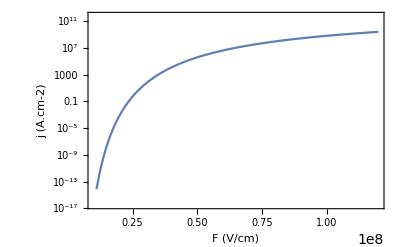

```mathematica
LogPlot[jMGFN0r[Freal,300,phi],{Freal,0,12*10^7},PlotRange->{{1*10^7,12*10^7},Automatic}, Frame-> True,GridLines-> Automatic, GridLinesStyle->Directive[Dotted, Gray],FrameLabel-> {"F (V/cm)","j (A.cm-2)"}]
```

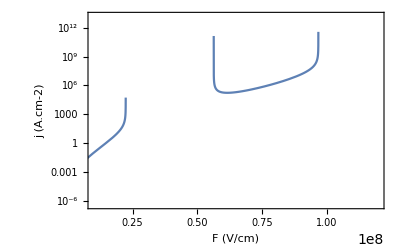

```mathematica
LogPlot[jMGRDr[Freal,1700,phi],{Freal,0,12*10^7},PlotRange->{{1*10^7,12*10^7},Automatic}, Frame-> True,GridLines-> Automatic, GridLinesStyle->Directive[Dotted, Gray],FrameLabel-> {"F (V/cm)","j (A.cm-2)"}]
```

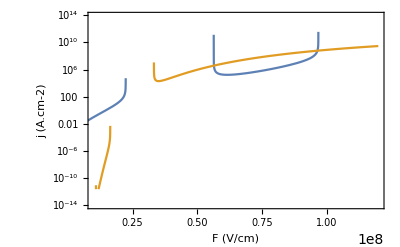

```mathematica
LogPlot[{jMGRDr[Freal,1700,phi],jMGFN0r[Freal,1700,phi]},{Freal,0,12*10^7},PlotRange->{{1*10^7,12*10^7},Automatic}, Frame-> True,GridLines-> Automatic, GridLinesStyle->Directive[Dotted, Gray],FrameLabel-> {"F (V/cm)","j (A.cm-2)"}]
```

```mathematica
(*Define j function depending on region of validity*)
```

```mathematica
region1[Freal_,Treal_,phi_]:=Re[function1[Freal,Treal]]> function2[Freal,Treal,paperE[phi]]&&Treal>(Freal/1103.04)^(3/4)&&Re[function3[Freal,Treal]]> function4[Freal,Treal]&&Treal>(Freal/1103.04)^(3/4)
region2[Freal_,Treal_,phi_]:=Re[functionFN1[Freal,Treal,phi]]> functionFN2[Freal,Treal,phi]&&Re[functionFN3[Freal,Treal,phi]]> functionFN4[Freal,Treal,phi]
```

```mathematica
jTOT[Freal_,Treal_,phi_]:=If[region1[Freal,Treal,phi],jMGRDr[Freal,Treal,phi],If[region2[Freal,Treal,phi],jMGFN0r[Freal,Treal,phi]]]
```

```mathematica
(*test to see if we are really in thermionic regime*)
jTOT[10^7,2000,4.5]/jMGRDr[10^7,2000,4.5]
```

1.

```mathematica
(*test to see if we are really in the field emission regime*)
jTOT[10^8,1000,4.5]/jMGFN0r[10^8,1000,4.5]
```

1.

```mathematica
(*so apparently it is working...*)
```

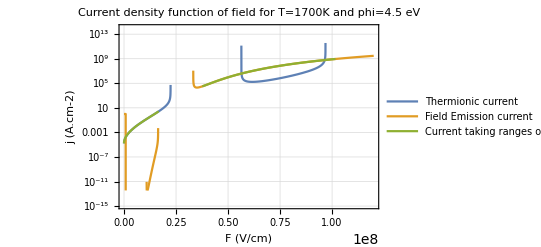

```mathematica
LogPlot[{jMGRDr[Freal,1700,phi],jMGFN0r[Freal,1700,phi], jTOT[Freal,1700,phi]},{Freal,0,12*10^7},PlotRange->{{0*10^7,12*10^7},Automatic}, Frame-> True,GridLines-> Automatic, GridLinesStyle->Directive[Dotted, Gray],FrameLabel-> {"F (V/cm)","j (A.cm-2)"},PlotLegends-> {"Thermionic current","Field Emission current","Current taking ranges of validity"}, PlotLabel->"Current density function of field for T=1700K and phi=4.5 eV\n"]
```

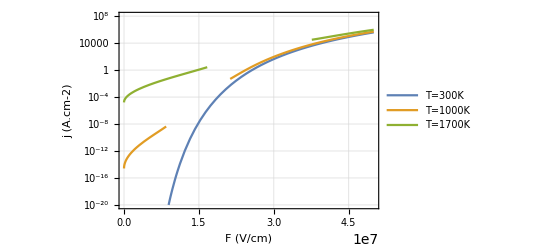

```mathematica
(*Replication of Murphy-Good Plot of Figure 7*)
LogPlot[{jTOT[Freal,300,phi],jTOT[Freal,1000,phi], jTOT[Freal,1700,phi]},{Freal,0,5*10^7},PlotRange->{{0*10^7,5*10^7},{10^(-20),10^8}}, Frame-> True,GridLines-> Automatic, GridLinesStyle->Directive[Dotted, Gray],FrameLabel-> {"F (V/cm)","j (A.cm-2)"},PlotLegends->{"T=300K","T=1000K","T=1700K"}]
```

```mathematica
(*ATTENTION, there is a BUG defining the regions, as the last plot fails to have the intermediate region. *)
```

```mathematica
(*define current function for logarithmic scale representation*)
logjTOT[Freal_,Treal_,phi_]:=Log[10,jTOT[Freal,Treal,phi]]
```

```mathematica
(*ATTENTION THIS PLOT TAKES 25 SECONDS TO BE GENERATED!!!*)
Plot3D[logjTOT[Freal,Treal,phi],
{Freal,0,12 10^7},{Treal,0,4000},
PlotRange-> {-20,10 },Ticks->{Automatic,Automatic,Table[{4*y,ToString[Round[10^(4*y),0.000000000000000000001]//ScientificForm//TraditionalForm]},{y,-20,8}]
},
WorkingPrecision-> 128, Mesh-> All, AxesLabel-> {"F (V/cm)","T (K)","      j (A.cm-2)"} , MaxRecursion-> 6](*//Timing*)
```

-Graphics3D-

```mathematica
newStyle[x_]:=x/.l_Line:>Sequence[Opacity[.8],Thick,Red,l]
```

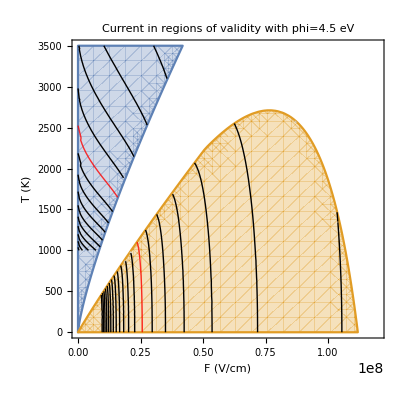

-Graphics-

```mathematica
Show [
RegionPlot[
{Re[function1[Freal,Treal]]> function2[Freal,Treal,paperE[phi]]&&Treal>(Freal/1103.04)^(3/4)&&Re[function3[Freal,Treal]]> function4[Freal,Treal]&&Treal>(Freal/1103.04)^(3/4),
Re[functionFN1[Freal,Treal,phi]]> functionFN2[Freal,Treal,phi]&&Re[functionFN3[Freal,Treal,phi]]> functionFN4[Freal,Treal,phi]
}, 
{Freal,0,12*10^7},{Treal,0,3500}, 
WorkingPrecision-> 32],
ContourPlot[logjTOT[Freal,Treal,phi],
{Freal,0,12 10^7},{Treal,0,3500},
WorkingPrecision-> 128, PlotRange->{-20,12}, Contours-> 20, MaxRecursion-> 2, AxesLabel-> {"F (V/cm)","T (K)"}, PlotLegends-> Automatic,FrameLabel->{"F (V/cm)","T (K)"}, ContourShading-> None, ContourLabels->Automatic]/.Tooltip[x_,0]:>Tooltip[newStyle[x],0],AxesLabel-> {"F (V/cm)","T (K)"}, FrameLabel->{"F (V/cm)","T (K)"},PlotLabel->"Current in regions of validity with phi=4.5 eV\n"]
```

4.5

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ∞ encountered.

Power::infy: Infinite expression 1/0.^3/4 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Infinity::indet: Indeterminate expression ComplexInfinity + ∞ encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater :: nord will be suppressed during this calculation.

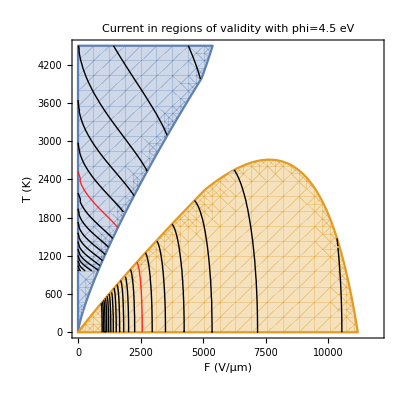

```mathematica
phi=4.5 (*eV*)
Show [
RegionPlot[
{Re[function1[Freal*(10^4),Treal]]> function2[Freal*(10^4),Treal,paperE[phi]]&&Treal>(Freal*(10^4)/1103.04)^(3/4)&&Re[function3[Freal*(10^4),Treal]]> function4[Freal*(10^4),Treal]&&Treal>(Freal*(10^4)/1103.04)^(3/4),
Re[functionFN1[Freal*(10^4),Treal,phi]]> functionFN2[Freal*(10^4),Treal,phi]&&Re[functionFN3[Freal*(10^4),Treal,phi]]> functionFN4[Freal*(10^4),Treal,phi]
}, 
{Freal,0,12*10^3},{Treal,0,4500}, 
WorkingPrecision-> 32, PlotRange->{{0,12 10^3},{0,4500}}],
ContourPlot[logjTOT[Freal*(10^4),Treal,phi],
{Freal,0,12 10^3},{Treal,0,4500},
WorkingPrecision-> 128, PlotRange->{-20,12}, Contours-> 20, MaxRecursion-> 2, AxesLabel-> {"F (V/μm)","T (K)"}, PlotLegends-> Automatic,FrameLabel->{"F (V/μm)","T (K)"}, ContourShading-> None, ContourLabels->Automatic, PlotRange->{{0,12 10^3},{0,4500},{-60,20}}]/.Tooltip[x_,0]:>Tooltip[newStyle[x],0],AxesLabel-> {"F (V/μm)","T (K)"}, FrameLabel->{"F (V/μm)","T (K)"},PlotLabel->"Current in regions of validity with phi=4.5 eV\n"]
```

```mathematica
(*Calculation of equations constants*)
kB (*eV/K*);
kBSI=1.38*10^(-23); (*m2 kg s-2 K-1*)
kBSIcm=kBSI*10^4;(*cm2 kg s-2 K-1*)
hbar (*eV.s*);
hbarSI=1.05*10^(-34); (*m2 kg s-1*)
hbarSIcm=hbarSI*10^4; (*cm2 kg s-1*)
meffGaAs=0.0662 *me;(*isotropic effective mass, FROM Martiensen, Springer Handbook of Condensed  Matter and Materials Data*)
```

```mathematica
Ry=(me*q^3/(4*Pi*ep0*hbarSI)^2)(*Rydberg constant in eV*)
```

27.3348

```mathematica
jquantum=(me^3*q^9/((hbarSI)^7)/(4*Pi*ep0)^4)/10^4(*current in A.cm-2*)
```

2.40584×10^14

```mathematica
Anorma=(q*me*kBSIcm^2)/(hbarSIcm^3*(2*Pi^2)) (*units of A.cm-2*)
```

121.345

```mathematica
AGaAs=(q*meffGaAs*kBSIcm^2)/(hbarSIcm^3*(2*Pi^2))
```

8.03304

```mathematica
RyGaAs=(meffGaAs*q^3/(4*Pi*ep0*hbarSI)^2)(*Rydberg GaAs constant in eV, defined with the effective mass of the GaAs ATTENTIOn, this DOES NOT HAVE THE MEANING OF THE RYDBERG CONSTANT, is just one attribution to facilitate!!!*)
```

1.80957

```mathematica
jquantumGaAs=(meffGaAs^3*q^9/((hbarSI)^7)/(4*Pi*ep0)^4)/10^4(*current quantum of hartree units in A.cm-2*)
```

6.97976×10^10

```mathematica
(*For a Working device OUTPUT current densities of 10^0 or 10^1 A.cm-2 are required*)
```

```mathematica
(*--------------NEW DEFINITION OF THE CORRECTION FACTORS*)
```

```mathematica
(*In semiconductors what will change is mainly the A constant, so the constant dividing the current!!! AND OTHE CONSTANTS AS WELL - SEE PAGE 130 of LOGBOOK*)
paperEGaAs[energy_]:=energy/RyGaAs;(*eV*)
```

```mathematica
(*THERMIONIC RD EQUATION *)
jMGRDGaAs[Freal_,Treal_,phi_]:=0.5*(paperEGaAs[kB*Treal]/Pi)^2*(Pi*dfunction[Freal,Treal]/Sin[Pi*dfunction[Freal,Treal]])*Exp[-(paperE[phi]-Sqrt[paperF[Freal]])/paperE[kB*Treal]](*in adim. units*)
jMGRDrGaAs[Freal_,Treal_,phi_]:=jMGRDGaAs[Freal,Treal,phi]*jquantumGaAs (*Amp.cm-2*)
```

```mathematica
(*FOWLER-NORDHEIM EQUATION*)
AFN=(q^2/(8*Pi*hbarSI*2*Pi)) (*units of A.eV.V-2*)
```

1.54394×10^-6

```mathematica
BFN[mass_]:=((8*Pi*Sqrt[2*mass])/(3*hbarSI*(2*Pi)*q))*(*in (V/m)/(J)^1.5*)(10^-2/((6.24*10^18)^(3/2))) (*units of (V/cm)/(eV)^1.5 THIS IS IN AGREEMENT WITH FORBES DATA*)
```

```mathematica
BFN[me]
```

6.86892×10^7

```mathematica
BFN[meffGaAs]
```

1.76733×10^7

```mathematica
(*Fowler-Nordheim Equation*)
```

```mathematica
jFN[Freal_,mass_,phi_]:=AFN*(Freal^2/phi)*Exp[-BFN[mass]*phi^1.5/Freal] (*Freal in units of amp.cm-2*)
```

```mathematica
(*SOME BANDSTRUCTURE CONSTANTS RELATIVE TO THE GALLIUM ARSENIDE, See Ioffe site in http://www.ioffe.rssi.ru/SVA/NSM/Semicond/GaAs/bandstr.html 
*)
Eg=1.424;(*eV*)
EgammaL=0.29;(*energy separation between gamma and L valleys in the bandstructure in eV*)
EgammaX=0.48;(*energy separation between gamma and X valleys in the bandstructure in eV*)
aGaAs=5.65*10^(-8);(*GaAs has zinc blende structure with lattice parameter in cm*)
```

```mathematica
ni[Treal_]:=Sqrt[Nc[Treal]*Nv[Treal]]*Exp[-Eg/(2*kB*Treal)](*intrinsic electron density*)
sigmai[Treal_,lattconst_]:=ni[Treal]*lattconst;(*surface electron density, for the case of intrinsic electron density in units of cm-2*)
sigma[n_,lattconst_]:=n*lattconst;(*surface electron density for the case where the doping is given as an argument*)
Nc[Treal_]:=(8.63 *10^15)*(1-1.93*10^(-4)*Treal-4.19*10^(-8)*Treal^2+21*Exp[-EgammaL/(2*kB*Treal)]+44*Exp[-EgammaX/(2*kB*Treal)])(*effective density of states in the conduction in cm-3*)
Nv[Treal_]:=(1.83*10^15)*Treal^1.5;(*effective density of states in the valence band in cm-3*)
```

ContourPlot::precw: The precision of the argument function ({0.000290118\ Im[If[Re[« 1 »] > Times[« 3 »] && Treal > Times[« 2 »] && Re[« 1 »] > Times[« 2 »] && Treal > Times[« 2 »], « 1 », If[region2[Times[« 2 »], Treal, 4.07], « 1 »]]] - 0}) is less than WorkingPrecision (128.).

ContourPlot::precw: The precision of the argument function ({0.000290118\ Re[If[Re[« 1 »] > Times[« 3 »] && Treal > Times[« 2 »] && Re[« 1 »] > Times[« 2 »] && Treal > Times[« 2 »], « 1 », If[region2[Times[« 2 »], Treal, 4.07], « 1 »]]] ≤ 0}) is less than WorkingPrecision (128.).

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ∞ encountered.

Power::infy: Infinite expression 1/0.^3/4 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

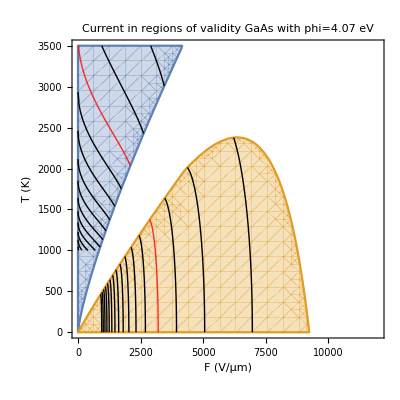

```mathematica
phiGaAs=4.07;
lineStyle={Thick,Black,Dashed};
Show [
RegionPlot[
{Re[function1[Freal*10^4,Treal]]> function2[Freal*10^4,Treal,paperE[phiGaAs]]&&Treal>(Freal*10^4/1103.04)^(3/4)&&Re[function3[Freal*10^4,Treal]]> function4[Freal*10^4,Treal]&&Treal>(Freal*10^4/1103.04)^(3/4),
Re[functionFN1[Freal*10^4,Treal,phiGaAs]]> functionFN2[Freal*10^4,Treal,phiGaAs]&&Re[functionFN3[Freal*10^4,Treal,phiGaAs]]> functionFN4[Freal*10^4,Treal,phiGaAs]
}, 
{Freal,0,12*10^3},{Treal,0,3500}, 
WorkingPrecision-> 32],
ContourPlot[Log[10,jTOT[Freal*10^4,Treal,phiGaAs]*jquantumGaAs/jquantum],
{Freal,0,12*10^3},{Treal,0,3500},
WorkingPrecision-> 128, PlotRange->{-20,12}, Contours-> 20, MaxRecursion-> 4, AxesLabel-> {"F (V/μm)","T (K)"}, PlotLegends-> Automatic,FrameLabel->{"F (V/μm)","T (K)"}, ContourShading-> None, ContourLabels->Automatic]/.Tooltip[x_,0]:>Tooltip[newStyle[x],0],AxesLabel-> {"F (V/μm)","T (K)"},
FrameLabel->{"F (V/μm)","T (K)"},
PlotLabel->"Current in regions of validity GaAs with phi=4.07 eV\n"]
```

Greater::nord: Invalid comparison with 0.  + 0.285918\ ⅈ attempted.

Greater::nord: Invalid comparison with 0.  + 0.357397\ ⅈ attempted.

Greater::nord: Invalid comparison with 0.  + 0.428876\ ⅈ attempted.

General::stop: Further output of Greater :: nord will be suppressed during this calculation.

ContourPlot::precw: The precision of the argument function ({0.000290118\ Im[If[Re[« 1 »] > Times[« 3 »] && Treal > Times[« 2 »] && Re[« 1 »] > Times[« 2 »] && Treal > Times[« 2 »], « 1 », If[region2[Times[« 2 »], Treal, 1], « 1 »]]] - 0}) is less than WorkingPrecision (128.).

ContourPlot::precw: The precision of the argument function ({0.000290118\ Re[If[Re[« 1 »] > Times[« 3 »] && Treal > Times[« 2 »] && Re[« 1 »] > Times[« 2 »] && Treal > Times[« 2 »], « 1 », If[region2[Times[« 2 »], Treal, 1], « 1 »]]] ≤ 0}) is less than WorkingPrecision (128.).

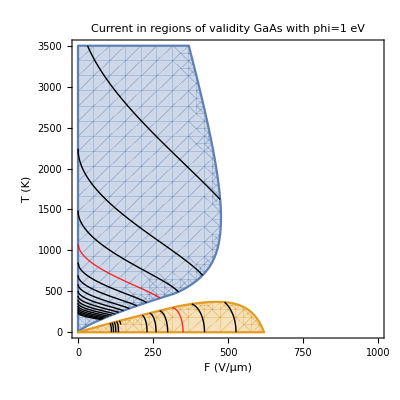

```mathematica
phiGaAs=1;
lineStyle={Thick,Black,Dashed};
Show [
RegionPlot[
{Re[function1[Freal*10^4,Treal]]> function2[Freal*10^4,Treal,paperE[phiGaAs]]&&Treal>(Freal*10^4/1103.04)^(3/4)&&Re[function3[Freal*10^4,Treal]]> function4[Freal*10^4,Treal]&&Treal>(Freal*10^4/1103.04)^(3/4),
Re[functionFN1[Freal*10^4,Treal,phiGaAs]]> functionFN2[Freal*10^4,Treal,phiGaAs]&&Re[functionFN3[Freal*10^4,Treal,phiGaAs]]> functionFN4[Freal*10^4,Treal,phiGaAs]
}, 
{Freal,0,1*10^3},{Treal,0,3500}, 
WorkingPrecision-> 32],
ContourPlot[Log[10,jTOT[Freal*10^4,Treal,phiGaAs]*jquantumGaAs/jquantum],
{Freal,0,1*10^3},{Treal,0,3500},
WorkingPrecision-> 128, PlotRange->{-20,12}, Contours-> 20, MaxRecursion-> 4, AxesLabel-> {"F (V/μm)","T (K)"}, PlotLegends-> Automatic,FrameLabel->{"F (V/μm)","T (K)"}, ContourShading-> None, ContourLabels->Automatic]/.Tooltip[x_,0]:>Tooltip[newStyle[x],0],AxesLabel-> {"F (V/μm)","T (K)"},
FrameLabel->{"F (V/μm)","T (K)"},
PlotLabel->"Current in regions of validity GaAs with phi=1 eV\n"]
```